```mathematica
db = DatabaseReference[FindFile[NotebookDirectory[]<>"/../data/genova.db"]]
```

DatabaseReference[…]

```mathematica
FetchData[filename_]:=  Import[NotebookDirectory[]<>"../data/simulation/"<>filename];
ExportData[filename_, data_]:= Export[NotebookDirectory[]<>"../data/simulation/"<>filename, data];
```

slots (extrema included) 93-101 205-222

```mathematica
totalCars = ExternalEvaluate[db, "
	SELECT  SUM(count_mean) as count, hour_slot as hour
	FROM traffic_data t
	GROUP BY hour_slot
;"];

max = Max[#["count"]& /@ Normal[totalCars] ];

bins = {#["hour"], #["count"] / max}& /@ Normal[totalCars] ;
binsPolar = { -#["hour"] * 2Pi / 288  +Pi/2,#["count"] / max}& /@ Normal[totalCars] ;

trafficPeaks = ListPolarPlot[
Callout[binsPolar, "(N (t))/N_max", {1, .8}, Appearance->"Line"],
Joined->False,
ColorFunction-> Function[{x,y,θ,r},(ColorData["SunsetColors"][1-r])],
PlotTheme->{"SerifLabels", "LargeLabels", "WarmColor"},
PlotStyle->PointSize[.015],
PlotLabel->"Traffic intensity during the day",
PolarGridLines->{{0, Pi, Pi/2, -Pi/2, -96/288*2Pi+Pi/2(*, -210/288*2Pi+Pi/2*)},{.5,  .96}},
PolarAxes->{True, True},
PolarTicks->{{ {Pi/2, "0:00"}, {0, "6:00"}, {-Pi/2, "12:00"}, {Pi, "18:00"}, {-96/288*2Pi+Pi/2, "8:00"}}, {.5, {1, 1}}},
PlotRange->{{-1.4, 1.4},{-1.2, 1.2}},
PolarAxesOrigin->{0, 1},
AxesStyle->Directive[Thick]
]
```

```mathematica
Export[NotebookDirectory[]<>"../assets/traffic-peaks.pdf", trafficPeaks]
```

C:\Users\Matteo\repo\uni\i-hate-badly-formatted-data\scripts\../assets/traffic-peaks.pdf

```mathematica
ListFitPlot[bins, PlotTheme->"Scientific", PlotFitElements->{"DataPoints", "BandCurves"}]
```

Before running this cell, create graph g in the other notebook!

```mathematica
g = FetchData["g.mx"];
A = AdjacencyMatrix[g];
deg = VertexDegree@g;

points = List@@@Normal@Counts@deg;
n = Total[points[[;;, 2]]];
fit = NonlinearModelFit[points, n*PDF[NormalDistribution[m,s], x], {m, s}, x];
fit["BestFitParameters"]
```

6464/1841

-Graphics-

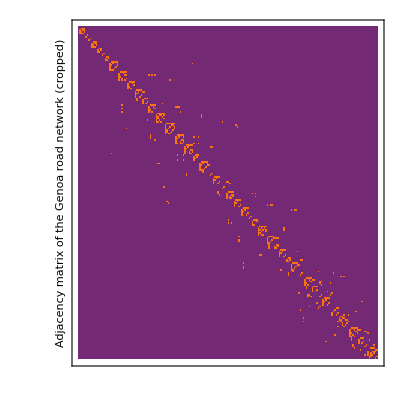

```mathematica
lambda = Mean[deg]
nullModelPlot =  ListLinePlot[
Callout[
Table[ PDF[PoissonDistribution[lambda], x], {x, 1, 20}],
"Poisson fit, λ=3.5",
{8, .1},
7,
CalloutStyle->Black,
LabelStyle->Medium
],
 PlotRange->Full,
PlotStyle->{Black, Dashed}
];

hist = Histogram[
deg,
{1},
"Probability",
PlotTheme->{"Classic", "FrameGrid", "LargeLabels", "SerifLabels"},
PlotRange->Full,
PlotLabel->"Node degree distribution of the\nGenoa road network",
FrameLabel->{"Node degree", "Probability"}
 ];

degreeDistribution = Show[hist, nullModelPlot]

gAdjPlot = MatrixPlot[
Normal@A[[;;200, ;;200]],
PlotTheme->{"Scientific", "LargeLabels", "Grid", "SerifLabels"},
FrameLabel->"Adjacency matrix of the Genoa road network (cropped)",
ColorFunction->  Function[{x},If[x==0, ColorData["SunsetColors"][.2], ColorData["SunsetColors"][.5]]],
ColorFunctionScaling->False,
GridLinesStyle->Directive[Gray, Dashed],
FrameTicks->None
]
```

```mathematica
Export[NotebookDirectory[]<>"../assets/degree-distribution.pdf", degreeDistribution]
Export[NotebookDirectory[]<>"../assets/adjacency-matrix.pdf", gAdjPlot]
```

C:\Users\Matteo\Desktop\repo\bazz\scripts\../assets/degree-distribution.pdf

C:\Users\Matteo\Desktop\repo\bazz\scripts\../assets/adjacency-matrix.pdf

Before running this cell, create mobilityDemandSpeed in notebook!

```mathematica
speedHist = Histogram[
speeds,
{10},
"Probability",
PlotTheme->{"Classic", "FrameGrid", "LargeLabels", "SerifLabels"},
PlotRange->Full,
PlotLabel->"Speed limit distribution of the\nGenoa road network",
FrameLabel->{"Road speed limit (km/h)", "Probability"}
]

gSpeedPlot = MatrixPlot[
Normal@mobilityDemandSpeed[[;;200, ;;200]],
PlotTheme->{"Scientific", "LargeLabels", "Grid", "SerifLabels"},
FrameLabel->"Speed-based mobility demand (cropped)",
ColorFunction->  Function[{x},If[x < .2, ColorData["SunsetColors"][.2], ColorData["SunsetColors"][x/2]]],
ColorFunctionScaling->False,
GridLinesStyle->Directive[Gray, Dashed],
FrameTicks->None
]
```

```mathematica
Export[NotebookDirectory[]<>"../assets/speed-distribution.pdf", speedHist]
Export[NotebookDirectory[]<>"../assets/speed-matrix.pdf", gSpeedPlot]
```

C:\Users\Matteo\repo\uni\i-hate-badly-formatted-data\scripts\../assets/speed-distribution.pdf

C:\Users\Matteo\repo\uni\i-hate-badly-formatted-data\scripts\../assets/speed-matrix.pdf

Before running this cell, create “times” in notebook!

```mathematica
hist = Histogram[
times,
{1},
"Probability",
PlotTheme->{"Classic", "FrameGrid", "LargeLabels", "SerifLabels"},
PlotRange->Automatic,
PlotLabel->"Travel time distribution in the\nGenoa road network",
FrameLabel->{"Single road travel time (s)", "Probability"}
];

points=Cases[hist,Rectangle[a_,b_,___]:>{Mean[{a[[1]],b[[1]]}],b[[2]]},All];
fit=NonlinearModelFit[points,PDF[ExponentialDistribution[l],x],{l},x];
fit["BestFitParameters"]

fitPlot = Plot[
Callout[
  Normal@fit, "Exponential fit, λ=0.15", {18, .08},
 15,
CalloutStyle->Red,
LabelStyle->Medium
],
 {x, 1, 25},
 PlotStyle->{Red}
];


timeHist = Show[hist, fitPlot]
```

{l→0.147426}

```mathematica
Export[NotebookDirectory[]<>"../assets/times-distribution.pdf", timeHist]
```

C:\Users\Matteo\repo\uni\i-hate-badly-formatted-data\scripts\../assets/times-distribution.pdf

Before running these cells, compute h_i in file! Also, exevute GetRoadCoordinates definition

```mathematica
hi = FetchData["h_i.mx"];
g = FetchData["g.mx"];
cols = ColorData["BlueGreenYellow"] /@(1-Rescale[Log/@hi]);
v = VertexList@g;
styles = Thread[v-> cols];
coords = GetRoadCoordinates@g;
data = {coords, cols} // Transpose;
```

```mathematica
i=0;
ProgressIndicator[Dynamic[i/Length[data]]]
bigPlot = GeoGraphics[
{
(i++;{
{PointSize[.003],#2, Point[#1]}
}
)&@@@data
},
GeoScaleBar->"Metric",
GeoProjection->"Orthographic",
GeoGridLines->Automatic,
GeoBackground->"VectorMonochrome",
ImageSize->{1414, 900}
];

hiPlot = Labeled[Legended[Rasterize[bigPlot, RasterSize->4000, ImageSize->Large], BarLegend[ ColorData["BlueGreenYellow"] [1-#]&, LegendLabel->"Log(h_j)/Max(Log(h_j))"]], "Geographical distributon of times to City Center", Top, LabelStyle->Large]
```

-Graphics-Geographical distributon of times to City Center

```mathematica
Export[NotebookDirectory[]<>"../assets/hi-plot.pdf", hiPlot]
```

C:\Users\Matteo\Desktop\repo\bazz\scripts\../assets/hi-plot.pdf

Before running these cells, compute roadThresholds in FIle

```mathematica
thresh = GetRoadThresholds[g];
hist = Histogram[
thresh,
{1},
"Probability",
PlotTheme->{"Classic", "FrameGrid", "LargeLabels", "SerifLabels"},
PlotRange->Automatic,
PlotLabel->"Critical car threshold distribution in the\nGenoa road network",
FrameLabel->{"Critical car number", "Probability"}
];

points=Cases[hist,Rectangle[a_,b_,___]:>{Mean[{a[[1]],b[[1]]}],b[[2]]},All];
fit=NonlinearModelFit[points,PDF[ExponentialDistribution[l],x],{l},x];
fit["BestFitParameters"]

fitPlot = Plot[
Callout[
  Normal@fit, "Exponential fit, λ=0.21", {12, .12},
 10,
CalloutStyle->Red,
LabelStyle->Medium
],
 {x, 1, 25},
 PlotStyle->{Red}
];


threshHist = Show[hist, fitPlot]
```

ParallelMap::nopar: No parallel kernels available; proceeding with sequential evaluation.

{l→0.211815}

```mathematica
Export[NotebookDirectory[]<>"../assets/thresholds-distribution.pdf", threshHist]
```

C:\Users\Matteo\repo\uni\i-hate-badly-formatted-data\scripts\../assets/thresholds-distribution.pdf

Stat probs

```mathematica
probs = FetchData["stat-probs.mx"];
cols = ColorData["SunsetColors"] /@(1-Rescale[Log/@probs]);
v = VertexList@g;
styles = Thread[v-> cols];
coords = GetRoadCoordinates@g;
data = {coords, cols} // Transpose;
```

```mathematica
i=0;
ProgressIndicator[Dynamic[i/Length[data]]]
bigPlot = GeoGraphics[
{
(i++;{
{PointSize[.003],#2, Point[#1]}
}
)&@@@data
},
GeoScaleBar->"Metric",
GeoProjection->"Orthographic",
GeoGridLines->Automatic,
GeoBackground->"VectorMonochrome",
ImageSize->{1414, 900}
];

probsPlot = Labeled[Legended[Rasterize[bigPlot, RasterSize->4000, ImageSize->Large], BarLegend[ ColorData["SunsetColors"] [1-#]&, LegendLabel->"Log(p_j)/Max(Log(p_j))"]], "Geographical distributon of stationary probabilities", Top, LabelStyle->Large]
```

-Graphics-Geographical distributon of stationary probabilities

```mathematica
Export[NotebookDirectory[]<>"../assets/probs-plot.pdf", probsPlot]
```

C:\Users\Matteo\Desktop\repo\bazz\scripts\../assets/probs-plot.pdf

## Sim results

### Multiple updates - congestion

```mathematica
PlotMultiSimHist[file_, title_] := (
coords = FetchData["coords.mx"];
filename = "results-"<>file;
vals = FetchData[filename<>".mx"];
thresholds = FetchData["thresholds.mx"];

stuckCars =Max[0, #1-#2] &@@@Transpose@{vals, thresholds};

hist = GeoHistogram[
WeightedData@@{coords, stuckCars},
100,
PlotTheme->{"Scientific", "FrameGrid"},
ColorFunction-> (ColorData["CherryTones"][1-#]&),
GeoScaleBar->"Metric",
GeoProjection->"Orthographic",
GeoGridLines->Automatic,
GeoBackground->"VectorMonochrome",
ImageSize->Large,
PlotLegends->BarLegend[Automatic, LegendLabel->Style["Number of cars\nover the threshold", TextAlignment->Center], LegendMargins->20],
PlotLabel->Style[title, FontSize->22]
];

{hist, filename<>".pdf"}
)

hists = {{"null", "naive", "speed", "time-morning", "time-evening"}, {"Congestion - Uniform Distribution", "Congestion - Naive Rates Simulation", "Congestion - Speed Rates Simulation", "Congestion - Time Rates Simulation (morning)", "Congestion - Time Rates Simulation (evening)"}} // Transpose;
hists = PlotMultiSimHist@@@(hists)
```

{{-Graphics-,results-null.pdf},{-Graphics-,results-naive.pdf},{-Graphics-,results-speed.pdf},{-Graphics-,results-time-morning.pdf},{-Graphics-,results-time-evening.pdf}}

```mathematica
Export[NotebookDirectory[]<>"../assets/"<>#2, #1] &@@@hists
```

{C:\Users\Matteo\Desktop\repo\bazz\scripts\../assets/results-null.pdf,C:\Users\Matteo\Desktop\repo\bazz\scripts\../assets/results-naive.pdf,C:\Users\Matteo\Desktop\repo\bazz\scripts\../assets/results-speed.pdf,C:\Users\Matteo\Desktop\repo\bazz\scripts\../assets/results-time-morning.pdf,C:\Users\Matteo\Desktop\repo\bazz\scripts\../assets/results-time-evening.pdf}

## Crossentropy computation

{-0.100825±0.000224703,-0.106019±0.000124578,-0.105483±0.000226137,-0.10599±0.000137519,-0.106067±0.0001346}

{null,naive,speed,time-morning,time-evening}

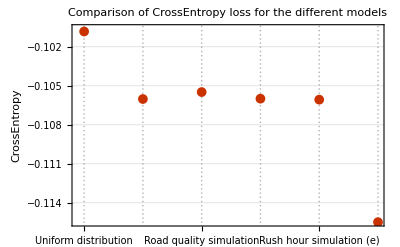

```mathematica
probs = FetchData["stat-probs.mx"];

On[Assert];

(*Crossentropy computation*)
ClearAll["H"];
H[file_, y_] := (
results = FetchData["results-"<>file<>".mx"];
hs = Table[
x = results[[n]];
x += 1; (*Ensure we have no -inf*)
x /= Total@x;


Assert[Length@x == Length@y];
arr = {y, x} // Transpose;
Total@(#1 Log[#2, E]&@@@ arr)
, {n, 1, Length@results}];
Mean@hs ± 3 StandardDeviation@hs
)
ce = H[#, probs] &/@ hists

hists = {"null", "naive", "speed", "time-morning", "time-evening"}
entropy = Total@(#1 Log[#2, E]&@@@ Transpose[{probs, probs}]);

legends = {"Uniform\ndistribution", "Lowest order\nsimulation", "Road quality\nsimulation", "Rush hour\nsimulation (m)", "Rush hour\nsimulation (e)", "Entropy\nof data"};
MakeLegend []:=Table[{i, Rotate[Style[legends[[i]], FontSize->12], 80Degree]}, {i, 1, 6}];

cePlot = ListPlot[
Append[ce, entropy],
PlotRange->All,
PlotTheme->{"Web", "FrameGrid", "LargeLabels", "SerifLabels"},
PlotLabel->"Comparison of CrossEntropy loss\nfor the different models",
FrameLabel->{"", "CrossEntropy"},
FrameTicks->{{Automatic, None}, {MakeLegend[], None}},
PlotMarkers->{Automatic, Medium}
]
```

```mathematica
Export[NotebookDirectory[]<>"../assets/crossentropy.pdf", cePlot]
```

C:\Users\Matteo\Desktop\repo\bazz\scripts\../assets/crossentropy.pdf

### Single update - Avalanche sizes

```mathematica
simulationResults = Import["resultsNaive.mx"];
avalancheSizes = simulationResults[[;;, ;;, 2]] // Flatten ;
hist = Histogram[
avalancheSizes,
{1},
 "Probability",
ScalingFunctions->{"Log", "Log"},
PlotRange->Full,
FrameLabel->{"Avalanche Size", "Probability"} ,
PlotTheme->{"Classic", "FrameGrid", "LargeLabels", "SerifLabels"},
PlotLabel->"Congestion avalanche size distribution"
];

points=Cases[hist,Rectangle[a_,b_,___]:>{Mean[{a[[1]],b[[1]]}],b[[2]]},All];
fit=LinearModelFit[points[[;;8]], {x}, x]
fit["BestFitParameters"]
fit["RSquared"]

fitPlot = Plot[
 Callout[Normal@fit, "R^2 = .93", {1.5, -4}, Appearance->"Line"],
 {x, -.5, 2.3},
 PlotStyle->{Red}
];


avalHist = Show[hist, fitPlot]
```

FittedModel[…]

{-0.774676,-3.12902}

0.929139

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"../assets/avalanche-dist.pdf", avalHist]
```

C:\Users\Matteo\Desktop\repo\bazz\scripts\../assets/avalanche-dist.pdf

### Single update - Avalanche geo distribution

```mathematica
coords = GetRoadCoordinates@g;
avalancheStartLocations = coords[[#]] &/@ Flatten@simulationResults[[;;, ;;, 1]] ;
avalancheGravity = {avalancheStartLocations, avalancheSizes / 30};
```

```mathematica
geoAvalHist = GeoHistogram[
WeightedData@@avalancheGravity, 100,
PlotTheme->{"Scientific", "FrameGrid"},
GeoScaleBar->"Metric",
GeoProjection->"Orthographic",
GeoGridLines->Automatic,
GeoBackground->"VectorMonochrome",
ImageSize->Large,
PlotLegends->BarLegend[Automatic, LegendLabel->Style["Average size of\navalanches starting \nin an area", TextAlignment->Center], LegendMargins->20],
PlotLabel->Style["Geographical distribution of avalanche gravity", FontSize->22]]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"../assets/avalanche-start.pdf",geoAvalHist]
```

### Congestion transition delay

```mathematica
thresholds = FetchData["thresholds.mx"];

congestedNodeCount = Table[
res = FetchData["results-time-morning-"<>ToString[n]<>".mx"];

Table[
Count[res[[x]] - thresholds, a_ /;a>0], {x, 1, Length@res}] / M
, {n, 4000, 32000, 4000}];

congestedNodeCountImm = Table[
res = FetchData["results-time-morning-immunized-900-"<>ToString[n]<>".mx"];

Table[
Count[res[[x]] - thresholds, a_ /;a>0], {x, 1, Length@res}]  /M
, {n, 4000, 32000, 4000}];

ticks = Table[n, {n, 4000, 32000, 4000}];

data1 = Callout[{ticks, Mean[#]±StandardDeviation[#]&/@congestedNodeCount} // Transpose, "Without immunization", {10000, .15}];
data2 = Callout[{ticks, Mean[#]±StandardDeviation[#]&/@congestedNodeCountImm } // Transpose, "With 5% immunized nodes", {25000, .05}];

immPlot = ListLinePlot[{data1,  data2},
FrameLabel->{"Number of cars on the road", "Fraction of congested nodes"} ,
PlotTheme->{"Classic", "FrameGrid", "LargeLabels", "SerifLabels"},
PlotLabel->"Congestion mitigation attempt results",
ImageSize->Large
]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"../assets/immunization-results.pdf",immPlot]
```

C:\Users\Matteo\Desktop\repo\bazz\scripts\../assets/immunization-results.pdf